```mathematica
(*IGNITION BOUND*)
```

```mathematica
(*WHITE DWARF WITH UNIFORM PROBABILITY DISTRIBUTION*)
```

```mathematica
R=5*10^6;(*in m*)
```

```mathematica
vesc=7.66*10^6;(*in m/sec*)
vbar=287.5*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*0.3(*in GeV/m^3*)(*Due to Overdensity*);
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=6*10^10;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
tage=2.83 10^17;(*in sec*)
```

```mathematica
fMBboosted[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ; 

b[mx_,sigmadmdm_]:=sigmadmdm*ρx/mx*NIntegrate[fMBboosted[u]/u*(vesc^2-u^2),{u,0,vesc}];
d[mx_,T_]:=π*rth[mx,T]^2*ρx/mx*NIntegrate[fMBboosted[u]/u*(vesc^2-u^2),{u,0,vesc}];
```

```mathematica
Nx0[mx_,T_]:=4/3 π R^3 ρx/mx;
```

```mathematica
tsat[mx_,sigmadmdm_,T_]:=1/b[mx,sigmadmdm]*Log[(π*rth[mx,T]^2)/(sigmadmdm*Nx0[mx,T])];(*estimate of saturation time which is the geometrical limit of self capture*)
```

```mathematica
totcap[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ]:=Piecewise[{{(π*rth[mx,T]^2)/sigmadmdm+(tage-tsat[mx,sigmadmdm,T])*d[mx,T],tsat[mx,sigmadmdm,T]-tage<0},{Nx0[mx,T]*Exp[b[mx,sigmadmdm]*tage],tsat[mx,sigmadmdm,T]-tage>0}}];
```

```mathematica
Qdiff=1.6 10^25 (ρ/10^12)^(4/15);(*GeV s^-1*)
```

```mathematica
NsgEtrans[mx_,T_]:=((4*π*rth[mx,T]^3*ρ)/(3*mx*1.78*10^-27))*mx/2*((4*π*ρ*G*rth[mx,T]^2)/(5*(3*10^8)^2));
```

```mathematica
delT[mx_,sigmadmdm_,T_]:=(4/3*π *rth[mx,T]^3)/(totcap[mx,sigmadmdm,T]*sigmadmdm*((kb*T)/(mx*1.78*10^-27))^0.5);
```

```mathematica
QDM[mx_,sigmadmdm_,T_]:=NsgEtrans[mx,T]/delT[mx,sigmadmdm,T];
```

```mathematica
Qdiff
```

7.55603×10^24

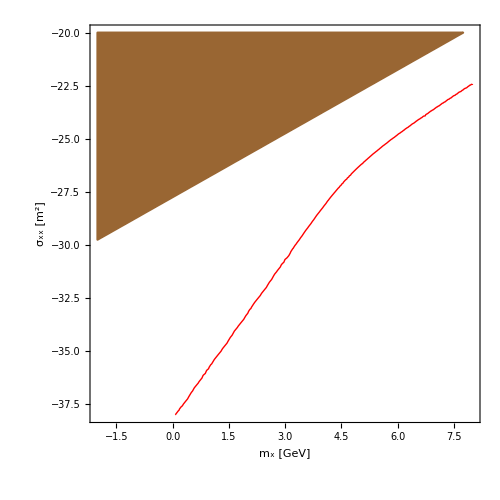

```mathematica
Show[ContourPlot[{QDM[10^x,10^y,10^7]==Qdiff},{x,-2,8},{y,-20,-38},PlotPoints->25,Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20],RegionPlot[10^y-1.78*10^-28*10^x>0,{x,-2,8},{y,-20,-38},Frame->True,PlotRangePadding->None,PlotStyle->Brown,BoundaryStyle->Brown]]
```

```mathematica
(*WHITE DWARF WITH GENERALIZED PROBABILITY DISTRIBUTION*)
```

```mathematica
R=5*10^6;(*in m*)
```

```mathematica
vesc=7.66*10^6;(*in m/sec*)
vbar=287.5*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=6*10^10;(*in kg/m^3*)
```

```mathematica
c=3*10^8;
mphi=10^-3;
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
tage=2.83 10^17;(*in sec*)
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ; 

g1[u_,mx_]:=(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2));

b[mx_?NumericQ,sigmadmdm_?NumericQ]:=sigmadmdm*NIntegrate[fMBboosted[u,mx]/u*(u^2+vesc^2)*(g1[u,mx]),{u,0,vesc},MaxRecursion->12];

d[mx_?NumericQ,T_?NumericQ]:=π*rth[mx,T]^2*NIntegrate[fMBboosted[u,mx]/u*(u^2+vesc^2)*(g1[u,mx]),{u,0,vesc},MaxRecursion->12];
```

```mathematica
Nx0[mx_?NumericQ,T_?NumericQ]:=4/3 π R^3 ρx/mx;
```

```mathematica
tsat[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ]:=1/b[mx,sigmadmdm]*Log[(π*rth[mx,T]^2)/(sigmadmdm*Nx0[mx,T])];

(*estimate of saturation time which is the geometrical limit of self capture*)
```

```mathematica
totcap[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ]:=Piecewise[{{(π*rth[mx,T]^2)/sigmadmdm+(tage-tsat[mx,sigmadmdm,T])*d[mx,T],tsat[mx,sigmadmdm,T]-tage<0},{Nx0[mx,T]*Exp[b[mx,sigmadmdm]*tage],tsat[mx,sigmadmdm,T]-tage>0}}];
```

```mathematica
Qdiff=1.6 10^25 (ρ/10^12)^(4/15);(*GeV s^-1*)
NsgEtrans[mx_,T_]:=((4*π*rth[mx,T]^3*ρ)/(3*mx*1.78*10^-27))*mx/2*((4*π*ρ*G*rth[mx,T]^2)/(5*(3*10^8)^2));
delT[mx_,sigmadmdm_,T_]:=(4/3*π *rth[mx,T]^3)/(totcap[mx,sigmadmdm,T]*sigmadmdm*((kb*T)/(mx*1.78*10^-27))^0.5);
QDM[mx_,sigmadmdm_,T_]:=NsgEtrans[mx,T]/delT[mx,sigmadmdm,T];
```

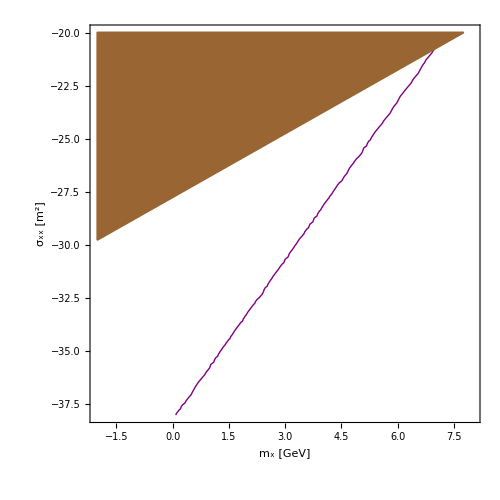

```mathematica
Show[ContourPlot[{QDM[10^x,10^y,10^7]==Qdiff},{x,-2,8},{y,-20,-38},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Purple}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20],RegionPlot[10^y-1.78*10^-28*10^x>0,{x,-2,8},{y,-20,-38},Frame->True,PlotRangePadding->None,PlotStyle->Brown,BoundaryStyle->Brown]]
```